```mathematica
Needs["ComputationalGeometry`"]
```

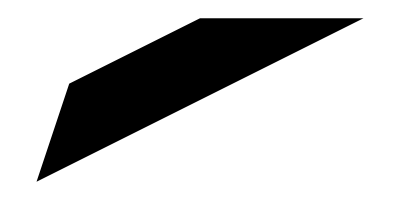

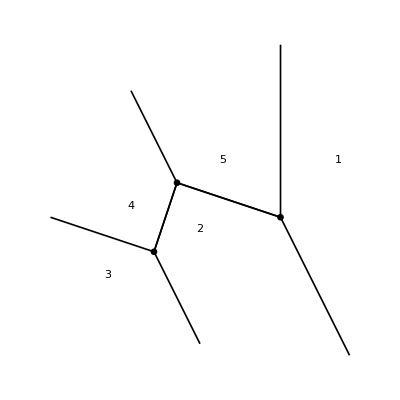

{{{2.,1.},{3.,4.},{7.5,2.5},Ray[{7.5,2.5},{10.5,-3.5}],Ray[{7.5,2.5},{7.5,10.}],Ray[{2.,1.},{4.,-3.}],Ray[{2.,1.},{-2.5,2.5}],Ray[{3.,4.},{1.,8.}]},{{1.,{3.,4.,5.}},{2.,{3.,2.,1.,6.,4.}},{3.,{1.,7.,6.}},{4.,{1.,2.,8.,7.}},{5.,{2.,3.,5.,8.}}}}

{{1,{5,2}},{2,{1,5,4,3}},{3,{2,4}},{4,{3,2,5}},{5,{4,2,1}}}

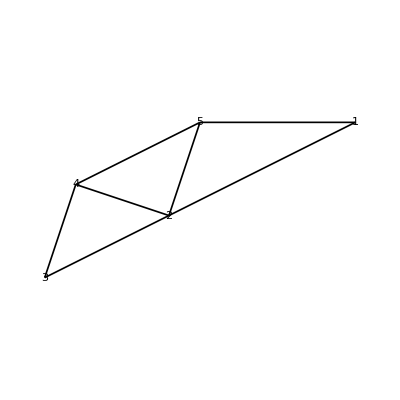

```mathematica
vertices = {{10,5},{4,2},{0,0},{1,3},{5,5}};
Graphics[Polygon[vertices]]
DiagramPlot[vertices]
VoronoiDiagram[vertices]//N
DelaunayTriangulation[vertices]
PlanarGraphPlot[vertices]
```